# MATH299M/CMSC389W - Visualization through Mathematica MIDTERM

It is expected that you work on this alone and show us what you have learned. You may freely reference our lessons and homeworks. Each problem should have a explanation in comments of your thought process for the problem and how you arrived at your solution. Good Luck!

For fill in the blank questions, the amount of underscores has no representation of the length nor number of characters to be expected to make code work properly. Furthermore, for fill in the blank questions, only blanks need to be filled in.

## Problem 1:

A Student submitted the following code and it has a error. Can you help the student solve their problem?

They gave the following description of their goal:

The following graph allows you to compare the Asymptotic Complexities of x^3, x^2, x, x log(x), and log(x). The options to the left of the graph allow you to add a coefficient to any function, and the text box allows you to add a constant term to the output of any function. The range slider allows you to change the Domain and Range that the graph draws.

The final output should look like this:

```mathematica
Manipulate[______[{a x^3 + h, b x^2 + i, c x + j, d x Log[x]+k, e Log[x] + l},{x, 0, r}, AspectRatio -> 1,PlotRange -> r, ________->{"x^3","x^2","x","x log(x)","log(x)"}, ________-> "Comparison of Asymptotic Complexities", ImageSize -> Large], {{a,1,"Coefficient x^3"},___,____}, {{b,1,"Coefficient x^2"},1,100},{{c,1,"Coefficient x"}, 1, 100},{{d,1,"Coefficient x log(x)"},___,____},{{e,1,"Coefficient Log[x]"},1,100},{{h,0,"Constant x^3"}},{{i,0,"Constant x^2"}},{{j,0,"Constant x"}},{{k,0,"Constant x log(x)"}},{{l, 0, "Constant log(x)"}},{{r,3,"Range"},1,1000},ControlPlacement -> Left]
```

## Problem 2:

Knowing how the arguments fit into a function is very important. As such here are the components to make a mollusc shell. Show your understanding of Parametric Plot 3D and demonstrate the final product:

```mathematica
{1.16^v Cos[v] (1+Cos[u])
```

```mathematica
MeshShading->{Opacity[0.4,Yellow]
```

```mathematica
-1.16^v Sin[v] (1+Cos[u])
-2 1.16^v (1+Sin[u])
```

```mathematica
Axes->False
```

```mathematica
{u,0,2 Pi}
```

```mathematica
MeshFunctions->{#1^2+#2^2&}
```

```mathematica
{v,-15,6}
```

```mathematica
PlotRange->All
```

```mathematica
Mesh->{{5}}
```

```mathematica
ParametricPlot3D[{_______,_____________,_______},________,_____________,____________,_____________,_________,Red},____________,_________,MaxRecursion->4]
```

## Problem 3:

A student was working to show the process of two waves (Sin, Cos) coming together he seems to have deleted some of his code and needs your assistance. 
In his head the model looks something like this:
-Graphics-

```mathematica
f[x_,t_,ω_,A_]:=If[x-t<-3π,A*Sin[ω(x-t)],0];
```

```mathematica
_____[Plot[f[_,_,Lω,LA]+f[-x,t,Rω,RA],{x,-4π,4π},______->{-4,4},_____-> 550,_____->Red],{{LA,1,"Left Amp"},0.1,3},{{Lω,1,"Left Ang Freq"},0.1,10},{{RA,1,"Right Amp"},0.1,3},{{Rω,1,"Right Ang Freq"},0.1,10},{t,0,10π},_______["Reset", {LA = 1,RA = 1, Lω = 1,Rω = 1,t = 0}],ControlPlacement->Left]
```

## Problem 4:

Use Manipulate to plot some function (any function) and a point on the function that you can manipulate with a slider. Here are the expected properties of the visualization:

You should be able to control the Min and Max value of  the plot domain. You can set the absolute min and absolute max value of the manipulate sliders to be whatever you feel necessary. Notice that in the provided picture, the minimum x value is -5 and the maximum x value is 38.8.

The point should follow the path along the function as you slide it around. (Hint: Figure out how to use ListPlot and Show to show the plot and the function at the same time)

The point should only slide between the min and max values you have set

Once completed, it should look a little something like this (again, any function is fine):

## Problem 5:

Extend off the 3D graph and contour example from Lecture 5 by allowing the user to input any arbitrary function of x and y into the Plot3D function and the ContourPlot function. Starter code is provided below.

```mathematica
Manipulate[GraphicsGrid[{{Plot3D[{x^2-y^2,c},{x,-5,5},{y,-5,5},ImageSize->Large,AspectRatio->1,PlotRange->{{-5.5,5.5},{-5.5,5.5},{-30,30}},PlotStyle->{Green,Orange}],ContourPlot[x^2-y^2==c,{x,-5,5},{y,-5,5},ImageSize->Large,AspectRatio->1]}}],
{c,-30,30}]
```

## Problem 6:

You’ve created an amazing plot showing off x^2 and x^3, but it still needs a bit more polish. 
Add text at the top and to the right of the given plot as shown in the figure below so your figure matches ours.

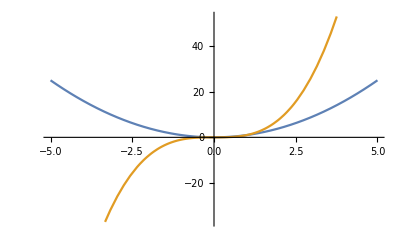

```mathematica
Plot[{x^2,x^3},{x,-5,5}]
```

## Problem 7:

Many programming languages often make a distinction between lists, sets, tuples, vectors, and matrices so you cannot use one in place of another. Does Mathematica do this? It is not enough to define each of the terms.

## Problem 8:

As the number of plot points increases in RegionPlot, ContourPlot, and others, the calculation of the plot becomes increasingly slow. What does the option PlotPoints do and why does doubling the number of plot points from 50 to 100 as opposed to from 25 to 50 result in such a significant slow down in two dimensional and three dimensional plots?

## Problem 9:

The following plot doesn’t look quite right! I’ve plotted f(x)=x which I expect to be at a 45° angle, but it isn’t. 
Fix the plot so f(x)=x is at exactly 45°.

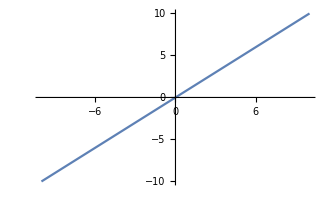

```mathematica
Plot[x,{x,-10,10}]
```

## Problem 10:

Mathematica contains shorthands for multiple commonly used functions and operations. Either give the alternate form or explain what the shorthand does (you only have to do one) for the following:

Shorthand a: /@

```mathematica
PrimeQ/@{2,3,4,5}
```

{True,True,False,True}

Shorthand b: @

```mathematica
Floor@7.3
```

7

Shorthand c: ?

```mathematica
?PrimeQ
```

## Problem 11:

The rotation matrix for rotating a point in 2-space around the origin is given as: (Cos[θ] | -Sin[θ]
Sin[θ] | Cos[θ]). So to actually use this, you would multiply a point (x,y) (represented as a vector) by the rotation matrix which would look like this:(Cos[θ] | -Sin[θ]
Sin[θ] | Cos[θ])(x
y)"="(x'
y').
(x'
y'), in other words, is the transformation of (x
y) by the rotation matrix or the rotation of (x
y) by θ radians.

Note that the following two lines express the same matrix/list; either form can be copy-pasted so you don’t have to type it out again.

```mathematica
{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}} (* manually typed out form *)
```

```mathematica
({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}) (* pretty-printed form *)
```

Create a rotation visualization by plotting points using ListPlot and then Manipulate θ so that we can see the points rotate around the origin as θ changes. (Hint: Make a function that takes in a θ and a point and returns the transformed point).

Note that to create a bunch of points quickly, you can do:

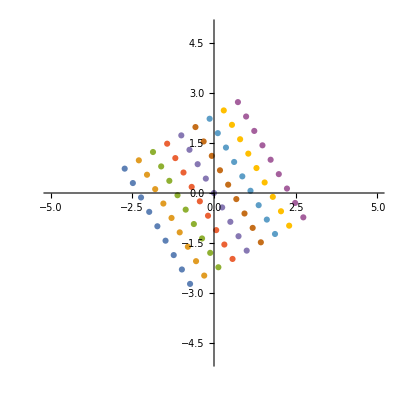

```mathematica
ListPlot[Table[({{Cos[π/6], -Sin[π/6]}, {Sin[π/6], Cos[π/6]}}).{x,y},{x,-2,2,0.5},{y,-2,2,0.5}],PlotRange->{{-5,5},{-5,5}},AspectRatio->1]
```

## Problem 12:

Use your new found graph skills to plot at least 3 functions and ensure that we know which is which. Hint: You will need to create a key to let us know which is which.

## Problem 13:

Use a manipulate to move a point around the unit circle. Hint: Use a ListPlot with a list of a single point to plot the point and make sure to set the plot range.
Below is the target plot. Your answer should have similar dimensions and we should not see the plot move, only the point should move.

## Problem 14:

We are now going to be interactive with manipulation! We are going to start from a very low spot and work our way to a complex alphabet manipulator using manipulate! This problem builds on itself and is used as a building block to see how deep your understanding of manipulate is. Credit will only be given up to the last level that you complete correctly. 
This is your starting block:

```mathematica
Style["a", FontSize -> 100, FontFamily -> "Times"]
```

a

Now  find a way to manipulate on the size of the letter a allowing us to START at 100 and have a LOWER limit of 1 and a UPPER limit of 200:

```mathematica
Manipulate[
Style["a", FontSize -> size, FontFamily -> "Times"],
{   ,    ,    }]
```

Well as nice as that was it simply does not satisfy the customer in question they want to use 3 different fonts:

```mathematica
Manipulate[
Style["a", FontSize -> size, FontFamily -> family],
{ ,  , },
{  , }
]
```

The customer is very happy with the progress that you are making and would like to expand to choosing and character in the English alphabet:

```mathematica
Manipulate[
Style["a", FontSize -> size, FontFamily -> family],
{ ,  , },
{  , },
{  , }
]
```

Meh the customer does not like the default control for picking the letters of the alphabet, he would rather have them all laid out in a straight line so that he may pick which he wants to manipulate:

```mathematica
Manipulate[
Style["a", FontSize -> size, FontFamily -> family],
{ ,  , },
{  , },
{  , ,  }
]
```

## Problem 15:

Once you finish the midterm, go to File > Save As... and save your midterm notebook as a PDF. Submit BOTH the notebook file and the PDF to ELMS.